Приложение Б.

```mathematica
Needs["Splines`"];
```

```mathematica
(*Введеём начальные значения, по которым будем строить сплайн*)
```

```mathematica
n=3;
```

```mathematica
Uzl={0.1,0.3,0.7,1.4};
```

```mathematica
Znach={1,-7,15,25};
```

```mathematica
Do[{Subscript[x, i]=Uzl⟦i+1⟧,Subscript[f, i]=Znach⟦i+1⟧},{i,0,n}]
```

```mathematica
Gr1=ListPlot[Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}],PlotStyle->{PointSize[0.02]},
PlotRange->{{0,1.5},{-60,60}}];
```

```mathematica
(*Построим сплайн второй степени с дефектом 1 - Subscript[S, 2,1](x)*)
```

```mathematica
Subscript[P, k_][X_]=Subscript[f, k]+(X-Subscript[x, k])*(Subscript[A, k]*X+Subscript[B, k]);
```

```mathematica
eq1=Table[Subscript[P, k][Subscript[x, k+1]]==Subscript[P, k+1][Subscript[x, k+1]],{k,0,n-2}];
```

```mathematica
eq2={Subscript[P, n-1][Subscript[x, n]]==Subscript[f, n]};
```

```mathematica
eq3=Table[Subscript[P, k]'[Subscript[x, k+1]]==Subscript[P, k+1]'[Subscript[x, k+1]],{k,0,n-2}];
```

```mathematica
eq4={Subscript[P, 0]'[Subscript[x, 0]]==0};
```

```mathematica
eq=Join[eq1,eq2,eq3,eq4];
```

```mathematica
koef = Solve[eq,{}]//Flatten
```

{A_0→-200.,A_1→337.5,A_2→-251.02,B_0→20.,B_1→-181.25,B_2→365.714}

```mathematica
Spl[X_]=Table[Subscript[P, k][X]/.koef,{k,0,n-1}]//Expand
```

{-1.+40. X-200. X^2,47.375-282.5 X+337.5 X^2,-241.+541.429 X-251.02 X^2}

```mathematica
Gr3=Table[Plot[Spl[X]⟦k⟧,{X,Subscript[x, k-1],Subscript[x, k]},PlotRange->All],{k,1,n}];
```

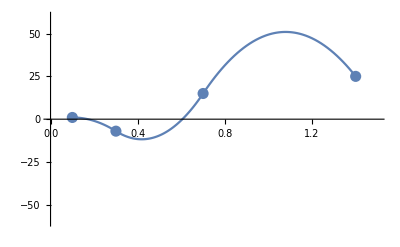

```mathematica
Show[Gr1,Gr3]
```